```mathematica
n  = 100;   (* number of molecules *)

r1 = {5,4,5};
r2 = {2,3,3};
r3 = {3,2,4};
```

```mathematica
n = 25;

Show[
Graphics3D[Table[    Table[{  Purple,Specularity[0.7,10] ,Ellipsoid[  { RandomReal[20], RandomReal[ 20] , z},  {r1,r2,r3 }  ]},{n}   ],{z,0,30,5}]],
Framed -> True,
ImageSize->Medium,
ViewPoint->{1.2,-4,0}
]
```

-Graphics3D-

```mathematica
n = 130;
Show[
Graphics3D[Table[ {  Purple,Specularity[0.7,10] ,Ellipsoid[  { RandomReal[20], RandomReal[ 20] , RandomReal[ 30]},  {r1,r2,r3 }  ]},{n}   ]],
Framed -> True,
ImageSize-> Medium,
ViewPoint->{1.2,-4,0}
]
```

-Graphics3D-

```mathematica
n = 30;

Show[
Graphics3D[Table[    Table[{  Purple,Specularity[0.7,10] ,Ellipsoid[  { RandomReal[20], RandomReal[ 20] , z},  {0.9, 0.9,3}  ]},{n}   ],{z,0,24,6}]],
Framed -> True,
ImageSize-> Medium,
ViewPoint->{1.2,-4,0}
]
```

-Graphics3D-

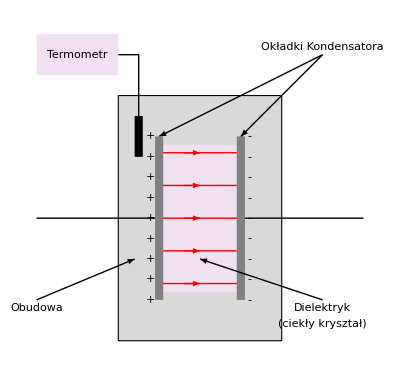

```mathematica
Show[

Graphics[ { LightGray, EdgeForm[Black],   Rectangle[{0,0},{2,3}]     }],
Graphics[ { Black, Thick,  Line[ { { -1,1.5}, {3,1.5} }],  Line[{ {0.25,2.5},{0.25, 3.5}, {0, 3.5} }]    } ],

Graphics[ { LightPurple,   Rectangle[{0.55,0.6},{1.45,2.4}]     }],
Table[  Graphics[{  Text[ "+", {0.4,n }],    Text[ "-", {1.6,n }]    }] ,{n,0.5,2.5,0.25}],
Table[  Graphics[ {Red, Thick, Arrow[{ {0.8,n}, {1,n}  }], Line[ { {0.5,n}, {1.45,n} }]    } ] , {n, 0.7, 2.6,0.4}],

Graphics[ { Gray,  Rectangle[{0.45,0.5},{0.55,2.5}],    Rectangle[{1.45,0.5},{1.55,2.5}]   }],

Graphics[ { LightPurple,   Rectangle[{-1,3.25},{0,3.75}]     }],
Graphics[ { Black,   Rectangle[{0.2,2.25},{0.3,2.75}], Text[ "Termometr", {-0.5, 3.5}]     }],

Graphics[{ Black,Thick, Arrowheads[0.05], Arrow[ { {2.5,3.5}, {0.5,2.5}}],   Arrow[ { {2.5,3.5}, {1.5,2.5} }], Text["Okładki Kondensatora", {2.5,3.6}]    } ],

Graphics[{ Black,Thick, Arrowheads[0.05], Arrow[ { {2.5,0.5}, {1,1}}], Arrow[ { {-1,0.5}, {0.2,1}}],
 Text["Dielektryk", {2.5,0.4}],  Text["(ciekły kryształ)", {2.5,0.2}] ,  Text["Obudowa", {-1,0.4}]}]
]
```